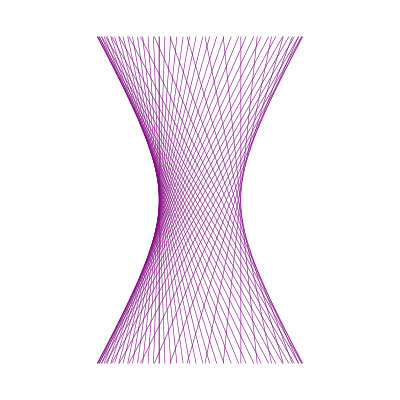

/Users/apple/Desktop/Mathematical graphics/双曲线.jpg

```mathematica
plt1=Table[ContourPlot[Cos[t]x+Sin[t]y-2x+2Cos[t]==1,{x,-4,4},{y,-4,4},ContourStyle->{Purple,Thickness[0.001]}],{t,-Pi,Pi,Pi/30}];
Show[plt1,Frame->False]
Export["/Users/apple/Desktop/Mathematical graphics/双曲线.jpg",%,ImageResolution->500]
```

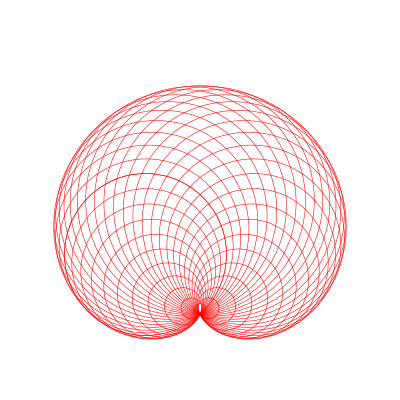

/Users/apple/Desktop/Mathematical graphics/蜗线.jpg

```mathematica
plt2=Table[ContourPlot[
(x-Cos[t])^2+(y-Sin[t])^2==Cos[t]^2+(Sin[t]+1.1)^2,
{x,-3,3},{y,-2,4},ContourStyle->{Red,Thickness[0.001]}],{t,-Pi,Pi,Pi/20}];
Show[plt2,Frame->False]
Export["/Users/apple/Desktop/Mathematical graphics/蜗线.jpg",%,ImageResolution->500]
```

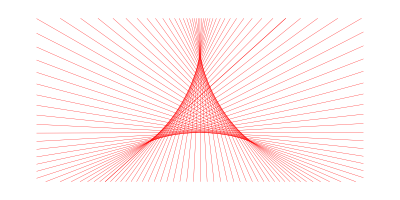

/Users/apple/Desktop/Mathematical graphics/三角星行线.jpg

```mathematica
plt3=Table[ContourPlot[
((Cos[t]-Sqrt[3]Sin[t]+Sqrt[3])/4-Cos[t])(y+1/2)==((-Sqrt[3]Cos[t]+3Sin[t]+1)/4+1/2)(x-Cos[t]),
{x,-4,4},{y,-1.7,2.3},ContourStyle->{Red,Thickness[0.0005]}],{t,-Pi+0.1,Pi+0.1,Pi/30}];
Show[plt3,AspectRatio->1/2,Frame->False]
Export["/Users/apple/Desktop/Mathematical graphics/三角星行线.jpg",%,ImageResolution->500]
```

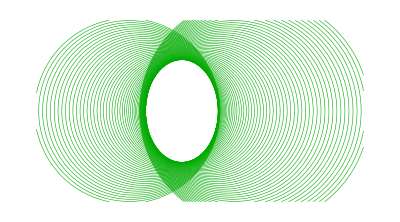

/Users/apple/Desktop/Mathematical graphics/椭圆.jpg

```mathematica
plt4=Table[ContourPlot[
(x-6+t)^2+y^2==(6-t)^2+(2-t)^2,
{x,-6,12},{y,-5,5},ContourStyle->{Darker[Green],Thickness[0.001]}],{t,0,7,0.1}];
Show[plt4, AspectRatio->10/18,Frame->False]
Export["/Users/apple/Desktop/Mathematical graphics/椭圆.jpg",%,ImageResolution->500]
```

π/50

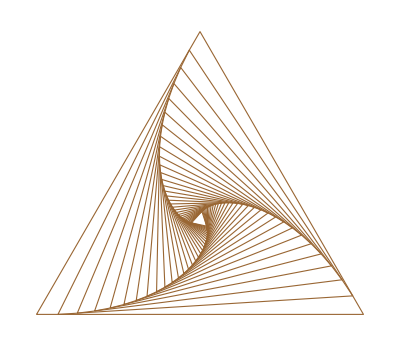

/Users/apple/Desktop/Mathematical graphics/追逐曲线1.jpg

```mathematica
t={-5Pi/6,-Pi/6,Pi/2,-5Pi/6};r=1;
plt5={};n=0;dt=Pi/50
While[n≤30,
plt5=Append[plt5,Graphics[{Thickness[0.002],Brown,Line[r Transpose[{Cos[t],Sin[t]}]]}]];
t=t+dt;r=Sin[Pi/6]/Sin[Pi/6+dt] r;
n++]
Show[plt5]
Export["/Users/apple/Desktop/Mathematical graphics/追逐曲线1.jpg",%,ImageResolution->500]
```

```mathematica
t={-5Pi/6,-Pi/6,Pi/2,-5Pi/6};r=1;
plt5={};n=0;dt=Pi/70
man=Manipulate[
While[n≤m,
plt5=Append[plt5,Graphics[{Thickness[0.002],Brown,Line[r Transpose[{Cos[t],Sin[t]}]]},ImageSize->500]];
t=t+dt;r=Sin[Pi/6]/Sin[Pi/6+dt] r;
n++];
Show[plt5],{m,0,50}]
```

π/70

Show::gtype: Symbol is not a type of graphics.

```mathematica
Export["/Users/apple/Desktop/test.gif",man,"ControlAppearance"->None]
(*Export["/Users/apple/Desktop/MMA/EnvelopeCurve/追逐曲线.gif",plt5]*)
```

/Users/apple/Desktop/test.gif